# Mathematica Project - Google Playstore App Download Prediction(MLR)

# Mathematica for Research

## Introduction

Working on Google Playstore Data - In this project, I will use Mathematica for predicting the installs i.e Downloads based on the Reviews and Ratings submitted by users and how the downloads get affected by this fields.

```mathematica
-Graphics--Graphics-
```

## Basics

The dataset used in this project contains - App, Category, Rating, Reviews, Size, Download, Type, Price, Content Rating, Genres, Last Updated, Current Version, Android Version

App - Contains name of the Apps.

Category - Contains different categories of the apps, For example - Social, Business, Game, Education, Entertainment etc.

Rating - Contains rating under 5 given by users.

Reviews - Contains number of reviews given by users.

Size - Contains size of the apps.

Download - Contains number of user downloaded the app.

Type - Contains type of app basically app is paid or free.

Price - Contains price of the apps.

Content Rating - Contains ratings which tells app is for everyone, kids or adults.

Android Version - Contains the android version supported by the apps.

Code to import the Dataset :-

```mathematica
data = Import["E:\\college\\Mathematica\\project\\googleplaystore.csv",HeaderLines->1];
App=data[[All,1]];
Category=data[[All,2]];
Rating=data[[All,3]];
Reviews=data[[All,4]];
Size=data[[All,5]];
Downloads=data[[All,6]];
Type=data[[All,7]];
Price=data[[All,8]];
ContentRating=data[[All,9]];
AndroidVersion=data[[All,10]];
```

## Filtering and Modifying Data for analysing

Removing Nan values from Ratings -

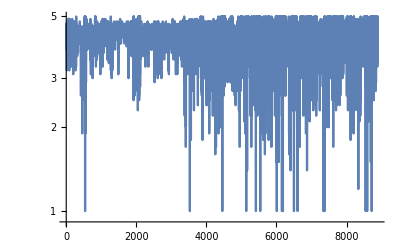

```mathematica
RatingsExcludingNaN = DeleteCases[Rating,"NaN"];
ListLinePlot[RatingsExcludingNaN,PlotRange->All,ScalingFunctions->"Log"]
```

Filtering Downloads by removing special characters by creating Rule -                                                                         -Graphics-

```mathematica
%//  Downloads
filtereddata= StringReplace[ToString[Downloads],{","->"","+"->""," "->","}];
ModDownloads = Flatten@ToExpression@StringSplit[filtereddata," "];
%// ModDownloads
```

{10,000+,500,000+,5,000,000+,50,000,000+,100,000+,50,000+,50,000+,1,000,000+,1,000,000+,10,000+,1,000,000+,1,000,000+,10,000,000+,100,000+,100,000+,5,000+,500,000+,10,000+,5,000,000+,10,000,000+,100,000+,100,000+,500,000+,100,000+,50,000+,10,000+,500,000+,10303,50,000+,500,000+,100+,100,000+,10,000+,5,000+,1,000+,50+,10+,100+,10,000+,100+,5,000,000+,5,000+,10,000+,10,000+,100,000+,5,000+,100,000+,1,000+,500+,10+,5,000+,100+,1,000+,1,000+,10,000,000+}[1]
 |  |  |  |

{10000,500000,5000000,50000000,100000,50000,50000,1000000,1000000,10000,1000000,1000000,10000000,100000,100000,5000,500000,10000,5000000,10000000,100000,100000,500000,100000,50000,10000,500000,100000,10000,100000,100000,50000,100000,100000,10000,100000,500000,5000000,10000,500000,10000,100000,10000000,100000,10000,10267,1000000,1000000,50,100000,5000,1000,10000,1000000,100000,100,500,100,50000,1000000,100,100,1000,10000,50000,500000,100,100000,10000,5000,1000,50,10,100,10000,100,5000000,5000,10000,10000,100000,5000,100000,1000,500,10,5000,100,1000,1000,10000000}[{1}]
 |  |  |  |

## Few plots using Mathematica to understand the data

This tells us the count of distinct categories of Apps

```mathematica
CountDistinct[Category]
```

33

```mathematica
%//DeleteDuplicates[Category]
```

```mathematica
{{{"ART_AND_DESIGN","AUTO_AND_VEHICLES","BEAUTY","BOOKS_AND_REFERENCE","BUSINESS","COMICS","COMMUNICATION","DATING","EDUCATION","ENTERTAINMENT","EVENTS","FINANCE","FOOD_AND_DRINK","HEALTH_AND_FITNESS","HOUSE_AND_HOME","LIBRARIES_AND_DEMO","LIFESTYLE","GAME","FAMILY","MEDICAL","SOCIAL","SHOPPING","PHOTOGRAPHY","SPORTS","TRAVEL_AND_LOCAL","TOOLS","PERSONALIZATION","PRODUCTIVITY","PARENTING","WEATHER","VIDEO_PLAYERS","NEWS_AND_MAGAZINES","MAPS_AND_NAVIGATION"}[1]}, {{{, , , , }}}}
```

Graph based on distinct categories of Apps :

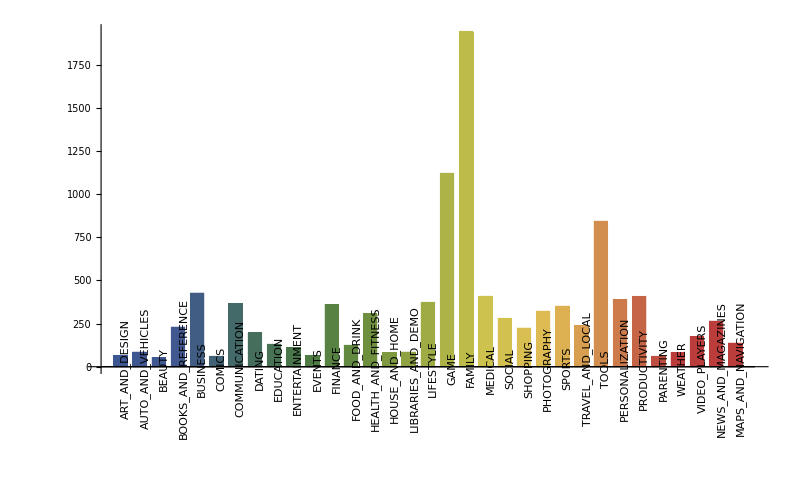

```mathematica
Show[BarChart[Counts[Category],ChartLabels->Placed[DeleteDuplicates[Category],Axis,Rotate[#,Pi/2]&] ,ChartStyle->"DarkRainbow"],ImageSize->800]
```

Our data contains “Family” types of apps more than any other types. 2nd highest category is “Games”.

This tells us the  distinct content rating of Apps

```mathematica
%//DeleteDuplicates[ContentRating]
```

{Everyone,Teen,Everyone 10+,Mature 17+,Adults only 18+,Unrated}[{Everyone,Teen,Everyone 10+,Mature 17+,Adults only 18+,Unrated}[{ART_AND_DESIGN,AUTO_AND_VEHICLES,BEAUTY,BOOKS_AND_REFERENCE,BUSINESS,COMICS,COMMUNICATION,DATING,EDUCATION,ENTERTAINMENT,EVENTS,FINANCE,FOOD_AND_DRINK,HEALTH_AND_FITNESS,5,MEDICAL,SOCIAL,SHOPPING,PHOTOGRAPHY,SPORTS,TRAVEL_AND_LOCAL,TOOLS,PERSONALIZATION,PRODUCTIVITY,PARENTING,WEATHER,VIDEO_PLAYERS,NEWS_AND_MAGAZINES,MAPS_AND_NAVIGATION}[{1}[1]]]]
 |  |  |  |

Graph based on distinct content rating of Apps :

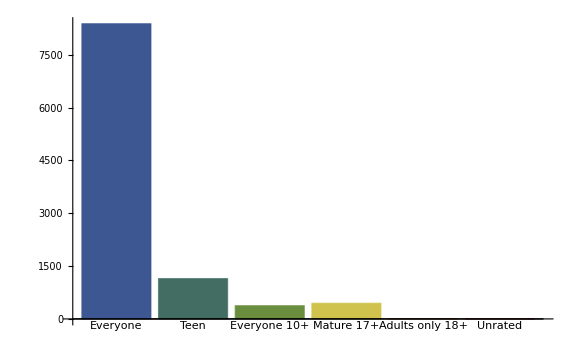

```mathematica
Show[BarChart[Counts[ContentRating],ChartLabels->Automatic ,ChartStyle->"DarkRainbow"],ImageSize->Large]
```

Our data contains major apps supported for “Everyone”.

Some 2D Graphs to understand the data   :                      -Graphics-

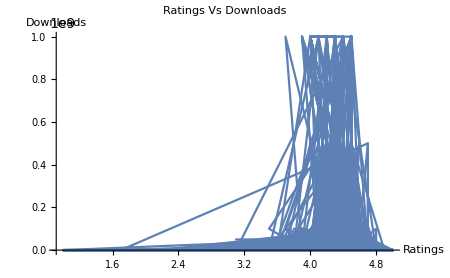

```mathematica
ListLinePlot[Transpose[{Rating,ModDownloads}],PlotRange->All,AxesLabel->{"Ratings","Downloads"},PlotLabel->"Ratings Vs Downloads",ImageSize->450]
```

Here we can see that for higher ratings i.e between 3.5 to 5 we see large amount of Downloads which means we need to check correlation between this two variables.

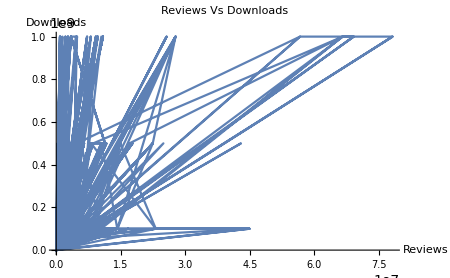

```mathematica
ListLinePlot[Transpose[{Reviews,ModDownloads}],PlotRange->All,AxesLabel->{"Reviews","Downloads"},PlotLabel->"Reviews Vs Downloads",ImageSize->450]
```

Here we can see as number of Reviews increases number of Downloads also increases which means we need to check correlation between this two variables.

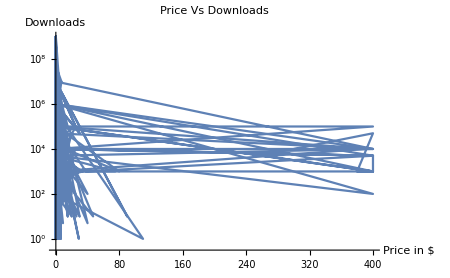

```mathematica
ListLinePlot[Transpose[{Price,ModDownloads}],PlotRange->Full,AxesLabel->{"Price in $","Downloads"},PlotLabel->"Price Vs Downloads",ImageSize->450,ScalingFunctions->"Log10"]
```

Here we can see as people generally prefer free apps over paid ones so we need to check col-linearity for Price too.

Analysing categorical variables through graphs   :

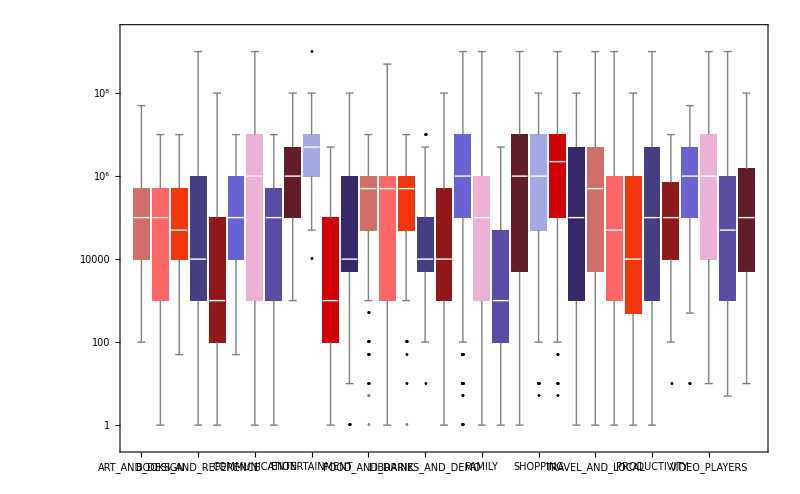

```mathematica
ds = Transpose[{Category,ModDownloads}];
BoxWhiskerChart[GatherBy[ds,# [[1]] &] [[All,All,2]],"Outliers",ImageSize->800,ChartStyle->56,ScalingFunctions->"Log",ChartLabels->Placed[DeleteDuplicates[ds[[All,1]]],Axis,Rotate[#,Pi/2]&]]
```

Category “Entertainment” has the higest median for Downloads which is 50,00,000  and Category “Business” and “Medical” has lowest median which is 1,000.

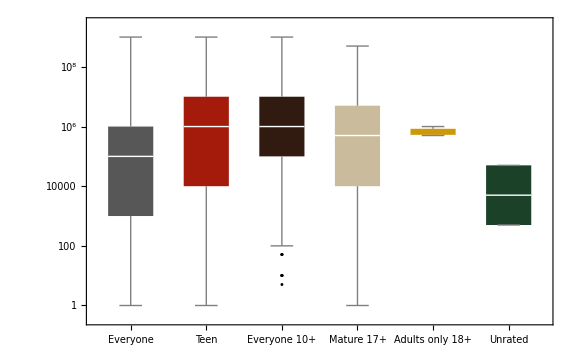

```mathematica
ds2 = Transpose[{ContentRating,ModDownloads}];
BoxWhiskerChart[GatherBy[ds2,# [[1]] &] [[All,All,2]],"Outliers",ImageSize->Large,ScalingFunctions->"Log",ChartStyle->6,ChartLabels->DeleteDuplicates[ds2[[All,1]]]]
```

Here “Teen” and “Everyone 10+” has highest median “1,000,000” and “Unrated” has lowest median about 25,250.

3D plot to analyse how Ratings and Reviews affect Downloads   :

```mathematica
ListPlot3D[Transpose[{Reviews,ModDownloads,Rating}],PlotRange->All,AxesLabel->{"Reviews","Downloads","Ratings"},ImageSize->Large]
```

-Graphics3D-

Here  as “Rating” and “Reviews” increases Download increases.

## Analysing the correlation between response variable with numerical predictor variable

The correlation coefficient is a statistical measure that calculates the strength of the relationship between the relative movements of two variables. The values range between -1.0 and 1.0. A calculated number greater than 1.0 or less than -1.0 means that there was an error in the correlation measurement. A correlation of -1.0 shows a perfect negative correlation, while a correlation of 1.0 shows a perfect positive correlation. A correlation of 0.0 shows no relationship between the movement of the two variables.

```mathematica
var1 = Normal[ModDownloads];
var2 = Normal[Rating /. "NaN" -> Mean[RatingsExcludingNaN]];
var3 = Normal[Reviews]; -Graphics-;
var4 = Normal[Price];
Correlation[var1,var2]
N[Correlation[var1,var3]]
Correlation[var1,var4]
```

0.0507554

0.634997

-0.0111467

Rating and Price have 0.05 and -0.01 correlation with Downloads which is very less, so we can say that this two factors doesn’t affect the Downloads much.
Review has correlation 0.63 with Downloads this means Downloads are affected by the number of reviews given by user.

## Checking multicollinearity before fitting model

```mathematica
Correlation[var2,var3]
Correlation[var3,var4]                                                                                                  -Graphics-
Correlation[var2,var4]
```

0.0686038

-0.00941703

-0.0205996

We can clearly see there is no multicollinearity between the  variables.

Different Plots to analyse how Reviews affect Downloads   :

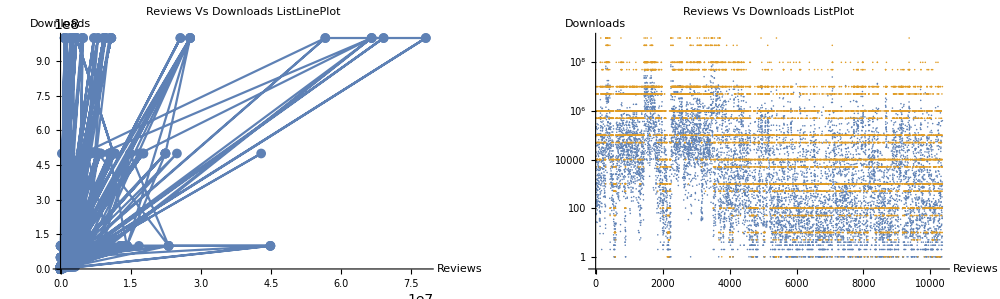

```mathematica
p1 = ListLinePlot[Transpose[{Reviews,ModDownloads}],PlotRange->All,AxesLabel->{"Reviews","Downloads"},PlotLabel->"Reviews Vs Downloads ListLinePlot",PlotMarkers->{Automatic, 10}];
p2 = ListPlot[{Reviews,ModDownloads}, PlotRange->All,ScalingFunctions->"Log",AxesLabel->{"Reviews","Downloads"},PlotLabel->"Reviews Vs Downloads ListPlot"];
GraphicsRow[{p1,p2},ImageSize->1000]
```

## Regression Model

Creating function to fit a Linear Model   :

```mathematica
dataToFit = Transpose[{ContentRating,Category,Reviews,ModDownloads}]; (* Fitting model with 2 categorical variable and 1 numerical variable *)
```

```mathematica
fitLinearModel[data_]:=LinearModelFit[data,{x1,x2,x3},{x1,x2,x3},NominalVariables->{x1,x2}];
lm = fitLinearModel[dataToFit]
```

FittedModel[-2.40496×10^6+«56»+2.13186×10^7 DiscreteIndicator[x2,VIDEO_PLAYERS,{ART_AND_DESIGN,AUTO_AND_VEHICLES,BEAUTY,BOOKS_AND_REFERENCE,BUSINESS,«23»,SPORTS,TOOLS,TRAVEL_AND_LOCAL,VIDEO_PLAYERS,WEATHER}]]

```mathematica
fitLinearModel2[data_]:=LinearModelFit[data,x1,x1];                     (* Fitting model with only numerical variable i.e Reviews *)
lm2 = fitLinearModel2[Transpose[{Reviews,ModDownloads}]]
```

FittedModel[6.48875×10^6+18.8936 x1]

Creating function to plot a Linear Model   :

```mathematica
LMPlot[model_] := ListPlot[model["BestFitParameters"],Frame->True,Filling->Axis] ;
LMPlot[lm]
```

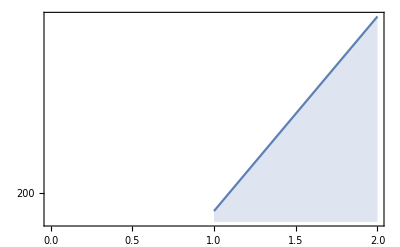

```mathematica
LMPlot2[model_] := ListPlot[model["BestFitParameters"],Frame->True,Joined->True,Filling->Axis,ScalingFunctions->"Reciprocal"] ;
LMPlot2[lm2]
```

Creating  Studentized Residual  plot of a  Linear Model  which  represents the list of studentized residuals  :

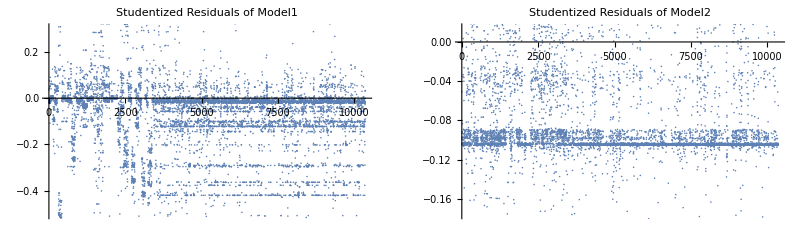

```mathematica
plot1 = ListPlot[lm["StudentizedResiduals"],PlotLabel->"Studentized Residuals of Model1"];
plot2 = ListPlot[lm2["StudentizedResiduals"], PlotLabel->"Studentized Residuals of Model2"];
GraphicsRow[{plot1,plot2},ImageSize->800]
```

Creating  Fit Residual  plot of a  Linear Model which  represents the residual errors for the fitted values  :

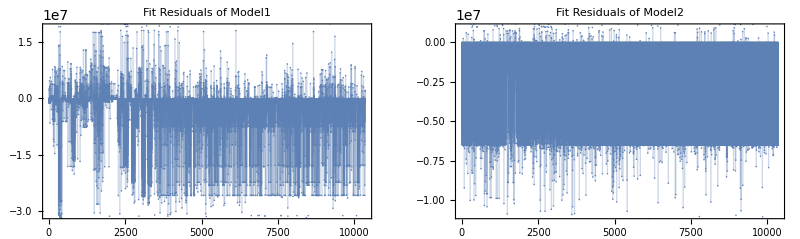

```mathematica
plot3= ListPlot[lm["FitResiduals"], Filling->Axis,PlotLabel->"Fit Residuals of Model1",Frame->True];
plot4 = ListPlot[lm2["FitResiduals"], Filling->Axis, PlotLabel->"Fit Residuals of Model2",Frame->True];
GraphicsRow[{plot3,plot4},ImageSize->800]
```

## Conclusion:

Creating summary function  :

```mathematica
SummaryFunction[model_]:={Print["\nANOVA Table for Model:       ",Quiet[model["ANOVATable"]]];
 Print["\nAdjustd R Squared Value:      ",model["AdjustedRSquared"]];
 Print["\nDurbin-Watson Test:           ",model["DurbinWatsonD"]];};
```

Summary of  model 1  :

```mathematica
SummaryFunction[lm];
```

ANOVA Table for Model:        | DF | SS | MS | F-Statistic | P-Value
x1 | 5 | 3.30093×10^17 | 6.60186×10^16 | 17.4976 | 2.68855×10^-17
x2 | 32 | 2.34318×10^18 | 7.32244×10^16 | 19.4074 | 9.15456×10^-107
x3 | 1 | 2.50727×10^19 | 2.50727×10^19 | 6645.29 | 0.
Error | 10318 | 3.89299×10^19 | 3.77301×10^15 |  | 
Total | 10356 | 6.66759×10^19 |  |  |

Adjustd R Squared Value:      0.413982

Durbin-Watson Test:           1.86333

The Adjusted R squared value is around 0.41 which means that the model is decent  for prediction. 
The Durbin-Watson test’s value is around 1.86, this indicate positive autocorrelation. SInce, The Durbin-Watson statistic will always have a value between 0 and 4. A value of 2.0 means that there is no autocorrelation detected in the sample. Values from 0 to less than 2 indicate positive autocorrelation and values from from 2 to 4 indicate negative autocorrelation.

Summary of  model 2  :

```mathematica
SummaryFunction[lm2];
```

ANOVA Table for Model:        | DF | SS | MS | F-Statistic | P-Value
x1 | 1 | 2.68852×10^19 | 2.68852×10^19 | 6996.5 | 0.
Error | 10355 | 3.97908×10^19 | 3.84266×10^15 |  | 
Total | 10356 | 6.66759×10^19 |  |  |

Adjustd R Squared Value:      0.403164

Durbin-Watson Test:           1.82089

The Adjusted R squared value is around 0.4 which means that the model is decent  for prediction. 
The Durbin-Watson test’s value is around 1.82, this indicate positive autocorrelation. SInce, The Durbin-Watson statistic will always have a value between 0 and 4. A value of 2.0 means that there is no autocorrelation detected in the sample. Values from 0 to less than 2 indicate positive autocorrelation and values from from 2 to 4 indicate negative autocorrelation.

Finally, we can conclude that Number of Downloads is dependent on Category, Content Rating and Reviews of the apps and rest other data i.e Price and Ratings doesn’t affect the Downloads as tested by calculating the correlation factor. We have also tested the Data by removing categorical variables “Category” and “Content Rating” and created the second model and found that categorical variables doesn’t have much significance over Downloads. So, we can say the number of Downloads of Apps depends on number of Reviews provided by the users.